### Predictions Charles' model

(WARNING : this is with neighbours' participation only, not the group mean (focal excluded))

```mathematica
monopop = {Subscript[τ, __]:>θ,τ̃->θ,τ̄->θ,nr->n,r->(1-m)^2/(1+(1-(1-m)^2)(n-1)),r̄->1/n+(1-1/n)r,n-> (f[θ,θ]-1)/γ};
```

```mathematica
SelectionGradient[θ_,Bb_,Cc_,fb_,m_,γ_]:=-2 Cc fb θ+(Bb fb (-1+m)^2 γ)/((-1+m)^2 (1+γ)-fb (2+(-2+m) m) (1+θ (Bb-Cc θ))+fb^2 (1+θ (Bb-Cc θ))^2);
```

Then, the following function Data[Bb, Cc, fb, m, η] solves numerically for internal candidate strategies, returning such strategies, θ, and the associated equilibrium local population size it

```mathematica
Data[Bb_,Cc_,fb_,m_,γ_]:=Block[{Singular},
Singular=FindRoot[SelectionGradient[θ,Bb,Cc,fb,m,γ],{θ,0.5,10^-6,1-10^-6}];
{θ,(fb (1-Cc θ^2+Bb θ)-1)/γ(*equilibrium local population size*)}//.Flatten[Singular]
]
```

```mathematica
predictionsCoopN=Table[Data[0.5,0.05,2,migrationValues[[i]],0.1], {i, Length[migrationValues]}]
```

{{0.224902,12.1984},{0.172669,11.6969},{0.129253,11.2758},{0.09333,10.9246},{0.0639763,10.6357},{0.0405606,10.404},{0.0226664,10.2261},{0.0100313,10.1002},{0.0025019,10.025}}

```mathematica
#[[1]]&/@ predictionsCoopN
```

{0.224902,0.172669,0.129253,0.09333,0.0639763,0.0405606,0.0226664,0.0100313,0.0025019}

```mathematica
predict = TableForm[Transpose[{migrationValues,#[[1]]&/@ predictionsCoopN,#[[2]]&/@ predictionsCoopN}]];
```

```mathematica
Export["/home/claire/institution-evolution/analyticalpredictions.txt",predict,"CSV"]
```

### Prediction my own PGG model

```mathematica
fecundity[τ_,τneighbours_]:=fb(1-c τ^2+b(1/n τ+(n-1)/n τneighbours));
```

```mathematica
κ[θ_]:=(1-m)^2/(n fecundity[θ,θ]-(1-m)^2(n-1));
migrationValues=Range[0.1,0.9,0.1];
numericalEquationsMigration=Table[(D[fecundity[τ,τneighbours],τ]+κ[θ] D[fecundity[τ,τneighbours],τneighbours]/.{τ->θ,τneighbours->θ,n-> (fecundity[θ,θ]-1)/γ})/.{fb->2,b->0.5,c->0.05,γ->0.1,m->migrationValues[[i]]}//FullSimplify,{i,Length[migrationValues]}];
cooperationPrediction=Table[FindRoot[numericalEquationsMigration[[i]]==0,{θ,0.5,10^-6,1-10^-6}],{i,Length[migrationValues]}];
demographyPrediction = Table[(fecundity[θ/.cooperationPrediction[[i]],θ/.cooperationPrediction[[i]]]-1)/γ/.{fb->2,c->0.05,b->0.5,γ->0.1}//FullSimplify, {i,Length[migrationValues]}]
```

```mathematica
D[fecundity[τ,τneighbours],τ]+κ[θ] D[fecundity[τ,τneighbours],τneighbours]/.{τ->θ,τneighbours->θ,n-> (fecundity[θ,θ]-1)/γ}//Simplify
```

-(fb (b^2 fb θ (-γ+2 c fb θ^2)+2 c θ ((-1+m)^2 (1+γ)+fb (2-2 m+m^2) (-1+c θ^2)+fb^2 (-1+c θ^2)^2)-b fb (γ-c γ θ^2+2 c θ^2 (2-2 fb-2 m+m^2+2 c fb θ^2))))/((-1+m)^2 (1+γ)-fb (2-2 m+m^2) (1+b θ-c θ^2)+fb^2 (1+b θ-c θ^2)^2)

```mathematica
predict = TableForm[Transpose[{migrationValues, θ/.cooperationPrediction, demographyPrediction}]]
```

0.1 | 0.49109
0.2 | 0.459828
0.3 | 0.435075
0.4 | 0.415503
0.5 | 0.400162
0.6 | 0.388367
0.7 | 0.379629
0.8 | 0.373609
0.9 | 0.370082

```mathematica
Export["/home/claire/institution-evolution-copy/analyticalpredictionspgg.txt",predict,"CSV"]
```

/home/claire/institution-evolution-copy/analyticalpredictions.txt

### Prediction my own policing model?

```mathematica
fecundity[τ0_,τ0neighbours_,τ1_,τ1neighbours_]:=fb((1-τ0)*r+b*(1-τ1)*r*(τ0+τ0neighbours*(n-1))/n-c*τ1*((1-τ0)^2)*r*(τ0+τ0neighbours*(n-1))/n);
```

```mathematica
κ[θ0_,θ1_]:=(1-m)^2/(n fecundity[θ0,θ0,θ1,θ1]-(1-m)^2(n-1));
```

```mathematica
gradient0=D[fecundity[τ0,τ0neighbours,τ1,τ1neighbours],τ0]+κ[θ0,θ1] D[fecundity[τ0,τ0neighbours,τ1,τ1neighbours],τ0neighbours]/.{τ0->θ0,τ0neighbours->θ0,τ1->θ1,τ1neighbours->θ1,n-> (fecundity[θ0,θ0,θ1,θ1]-1)/γ}/.{fb->2,b->0.5,c->0.05,γ->0.1,r->1,m->0.1}
```

2 (-1+(0.05 (1-θ1))/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))-(0.005 (1-θ0)^2 θ1)/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))+(0.01 (1-θ0) θ1 (θ0+θ0 (-1+10. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)))))/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)))+(1.62 ((0.05 (1-θ1) (-1+10. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))))/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))-(0.005 (1-θ0)^2 θ1 (-1+10. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))))/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))))/(-0.81 (-1+10. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)))+20. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)) (1-θ0+(0.05 (1-θ1) (θ0+θ0 (-1+10. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)))))/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))-(0.005 (1-θ0)^2 θ1 (θ0+θ0 (-1+10. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)))))/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))))

```mathematica
gradient1=D[fecundity[τ0,τ0neighbours,τ1,τ1neighbours],τ1]+κ[θ0,θ1] D[fecundity[τ0,τ0neighbours,τ1,τ1neighbours],τ1neighbours]/.{τ0->θ0,τ0neighbours->θ0,τ1->θ1,τ1neighbours->θ1,n-> (fecundity[θ0,θ0,θ1,θ1]-1)/γ}/.{fb->2,b->0.5,c->0.05,γ->0.1,r->1,m->0.1}
```

2 (-(0.05 (θ0+θ0 (-1+10. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)))))/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n))-(0.005 (1-θ0)^2 (θ0+θ0 (-1+10. (-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)))))/(-1+2 (1-θ0+(0.5 (θ0+(-1+n) θ0) (1-θ1))/n-(0.05 (1-θ0)^2 (θ0+(-1+n) θ0) θ1)/n)))

```mathematica
g0[x_]:=gradient0/.{θ0->0.5,θ1->x}//FullSimplify
```

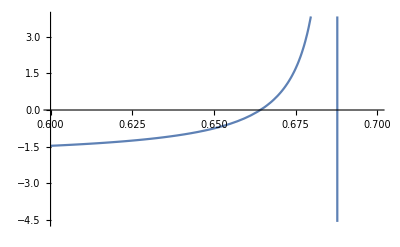

```mathematica
Plot[g0[i], {i,0.6,0.7}, PlotRange->Automatic]
```

```mathematica
FindRoot[g0[θ0]==0,{θ0,0.66,10^-6,1-10^-6}]
```

{θ0→0.664173}

```mathematica
g1[x_]:=gradient1/.{θ0->0.5,θ1->x}//FullSimplify
```

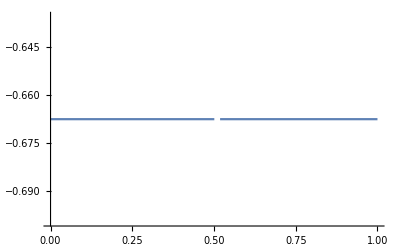

```mathematica
Plot[g1[i], {i,0,1}, PlotRange->Automatic]
```

```mathematica
FindRoot[g1[θ1]==0,{θ1,0.5,10^-6,1-10^-6}]
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {θ1} = {0.5}.

FindRoot[g1[θ1]==0,{θ1,0.5,1/10^6,1-1/10^6}]

```mathematica
g1[0.7]
```

-0.66763

```mathematica
g0=gradient0//FullSimplify
g1=gradient1//FullSimplify
```

(2342.+220. θ1+θ0 (-6622.+(6280.-2000. θ0) θ0+(-7908.4+θ0 (16276.8+θ0 (-11154.4+(3304.-800. θ0) θ0))) θ1+(-363.+θ0 (8734.22+θ0 (-12492.7+θ0 (6863.26+θ0 (-3054.22+(612.4-120. θ0) θ0))))) θ1^2+θ0 (133.1+θ0 (-3506.58+θ0 (3280.2+θ0 (-2440.6+θ0 (895.9+θ0 (-302.5+(48.48-8. θ0) θ0)))))) θ1^3+θ0^3 (266.2+θ0 (-411.4+θ0 (244.2+θ0 (-127.+θ0 (37.+θ0 (-10.2+(1.4-0.2 θ0) θ0)))))) θ1^4))/((-10.+θ0 (10.+(11.+θ0 (-2.+1. θ0)) θ1)) (127.1+θ0 (-219.-240.9 θ1+θ0 (100.+θ1 (263.8+121. θ1+θ0 (-61.9-44. θ1+θ0 (20.+(26.+θ0 (-4.+1. θ0)) θ1)))))))

(θ0 (11.+θ0 (-13.-12.1 θ1+θ0 (3.+4.4 θ1+θ0 (-1.+(-2.6+(0.4-0.1 θ0) θ0) θ1)))))/(-10.+θ0 (10.+(11.+θ0 (-2.+1. θ0)) θ1))

```mathematica
FindRoot[{g0== 0,g1==0},{{θ0,0.35,10^-6,1-10^-6},{θ1,0.8,10^-6,1-10^-6}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{θ0→0.294445,θ1→1.×10^-6}

```mathematica
g1/.{θ0->0.29444474643326574,θ1->1.*^-6}
```

-0.309102

```mathematica
g0[x_]=gradient0/.{θ1->x}//FullSimplify
```

(2342.+θ0 (-6622.+(6280.-2000. θ0) θ0)+x (220.+θ0 (-7908.4+θ0 (16276.8+θ0 (-11154.4+(3304.-800. θ0) θ0))))+x^2 θ0 (-363.+θ0 (8734.22+θ0 (-12492.7+θ0 (6863.26+θ0 (-3054.22+(612.4-120. θ0) θ0)))))+x^3 θ0^2 (133.1+θ0 (-3506.58+θ0 (3280.2+θ0 (-2440.6+θ0 (895.9+θ0 (-302.5+(48.48-8. θ0) θ0))))))+x^4 θ0^4 (266.2+θ0 (-411.4+θ0 (244.2+θ0 (-127.+θ0 (37.+θ0 (-10.2+(1.4-0.2 θ0) θ0)))))))/((-10.+θ0 (10.+x (11.+θ0 (-2.+1. θ0)))) (127.1+θ0 (-219.+100. θ0+x (-240.9+θ0 (263.8+θ0 (-61.9+20. θ0)+x (121.+θ0 (-44.+θ0 (26.+θ0 (-4.+1. θ0)))))))))

```mathematica
Table[FindRoot[g0[i]==0,{θ0,0.5,10^-6,1-10^-6}],{i,0.1,0.9,0.1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{θ0→0.959595},{θ0→0.879244},{θ0→0.81114},{θ0→0.752651},{θ0→0.701915},{θ0→0.657584},{θ0→0.618734},{θ0→0.585},{θ0→0.558405}}